Analiza danych z qc

```mathematica
path = "/home/jakub/Developer/qc/qc/files/";
outNames = FileNames["*", path<>"outputs"];
files = Table[Flatten@Import[outNames[[i]], "TSV"], {i, 1, Length@outNames}];
outBaseNames = ToExpression@Table[StringSplit[FileNameTake[outNames[[i]]], "V"], {i, 1, Length@outNames}];
data = Dataset@Table[<|"l"-> outBaseNames[[i]][[1]], "v"-> outBaseNames[[i]][[2]], "d"->files[[i]]|>, {i, 1, Length@outNames}];
means = Dataset@Table[<|"l"-> outBaseNames[[i]][[1]], "v"-> outBaseNames[[i]][[2]], "d"->Mean[data[All,"d"][[i]]]|>,{i,1,Length@files}]
```

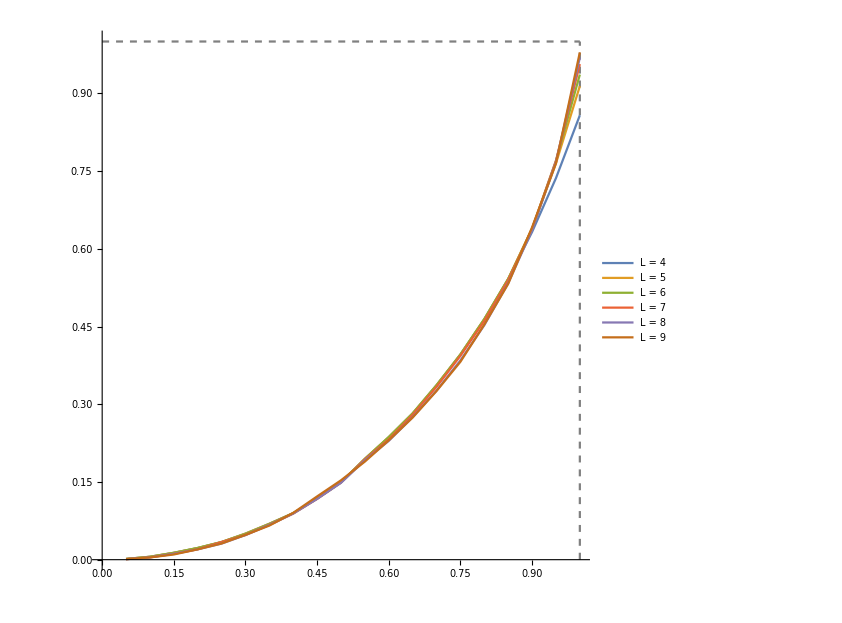

```mathematica
vis =Table[ Transpose[outBaseNames][[2]][[i;;i+19]], {i, 1, 120, 20}];
bestT = Table[data[i;;i+19,"d", Mean], {i, 1, 120,20}];
bestT = Transpose@Table[bestT[[i]][[j]], {j, 1, Length@bestT[[1]]}, {i, 1, Length@bestT}];
plotPoints = Table[Transpose@{vis[[i]], bestT[[i]]}, {i, 1, Length@vis}];
plots = Show[ParametricPlot[{x,1}, {x,0,1}, PlotStyle->{Gray,Dashed}],ParametricPlot[{1,y}, {y,0,1}, PlotStyle->{Gray,Dashed}],ListLinePlot[plotPoints, PlotLegends->Placed[{"L = 4", "L = 5", "L = 6", "L = 7", "L = 8", "L = 9"},{0.6,0.7}], AxesLabel->{"visibility", "t"}], PlotRange->Full]
```

```mathematica
Export[path<>"figures/plot.png", plots, "PNG", RasterSize-> 2000];
```